## Исходные данные :

### Параметры :

Весовые коэффициенты:

```mathematica
ϵ1=1/N[#]&;
```

```mathematica
ϵ2=1/N[100*#]&;
```

Количество обучающих итераций, после которых происходит обновление классов:

```mathematica
λ=200;
```

Общее количество итераций (>= λ):

```mathematica
nOfi=600;
```

Возраст дуги, по истечении которого ее следует удалить:

```mathematica
ageMax=50;
```

Параметры, которые контролируют процесс удаления "шумовых" узлов:

```mathematica
c1=0.0001;
c2=1.0;
```

Максимально возможное количество связей для узла:

```mathematica
numberOfEdges=Infinity;
```

Инициализация количества классов:

```mathematica
classCount=0;
```

Счетчик классов и узлов:

```mathematica
classId=1;
nodeId=1;
```

### Создадим решетку:

```mathematica
LatticeData[]//TableForm//Framed
```

BaseCenteredMonoclinic
BaseCenteredOrthorhombic
BodyCenteredCubic
BodyCenteredOrthorhombic
CenteredTetragonal
CoxeterTodd
FaceCenteredCubic
FaceCenteredOrthorhombic
HexagonalClosePacking
HexagonalLattice
KorkineZolotarev
Leech
SimpleCubic
SimpleHexagonal
SimpleMonoclinic
SimpleOrthorhombic
SimpleTetragonal
SimpleTriclinic
SimpleTrigonal
SquareLattice
TetrahedralPacking

Размер решетки:

```mathematica
P=20;
```

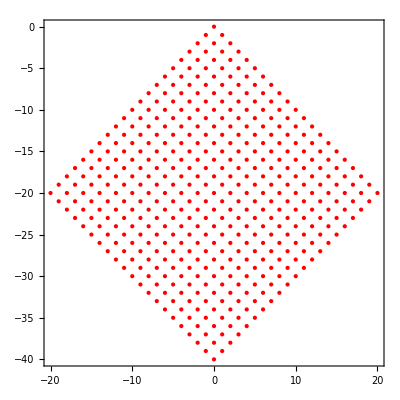

```mathematica
l=Normal@LatticeData["FaceCenteredCubic","Basis"];
latVec=Cases[l,{a_Integer,b_Integer,c_Integer}/;c==0->{a,b}];(*2D*)
lattice=Flatten[Table[i latVec[[1]]+j latVec[[2]],{i,0,P},{j,0,P}],1];
Graphics[{Red,PointSize[Large],Point@lattice},Frame->True,AspectRatio->1]
```

## Работа алгоритма ESOINN :

### Набор промежуточных функций:

Вспомогательные функции:

```mathematica
findMinAndMax[firstWinner_Association,secondWinner_Association]:=Module[
{minId,maxId},
If[firstWinner⟦"node id"⟧≤secondWinner⟦"node id"⟧,

minId=firstWinner⟦"node id"⟧;
maxId=secondWinner⟦"node id"⟧;
{minId,maxId},

maxId=firstWinner⟦"node id"⟧;
minId=secondWinner⟦"node id"⟧;
{minId,maxId}
]
]
```

```mathematica
findPositionInNodes[node_Association]:=Module[
{
nodesId=#⟦"node id"⟧&/@nodes,
nodeId=node⟦"node id"⟧
},
Part[Flatten[Position[nodesId,nodeId]],1]
]
```

Добавление узла:

```mathematica
newNode[{x_,y_}]:=<|
"node id"->nodeId++,(*Warning! Uses global variable!*)
"coords"->{N@x,N@y},
"error"->0,
"number of wins"->0,
"possible number of edges"->numberOfEdges,
"density"->0,
"class id"->Null,
"points"->0
|>
```

Пороговое значение:

```mathematica
threshold[node_Association]:=Module[
{
coords,
nodeCoords=node⟦"coords"⟧,
tempCoords,
connectionsCoords=#⟦"coords"⟧&/@getConnectedNodes[node]
},
If[connectionsCoords=={},

coords=#⟦"coords"⟧&/@nodes;
tempCoords=PadRight[{nodeCoords},Length[coords],{nodeCoords}];
Min@Cases[x_/;x≠0][MapThread[EuclideanDistance,{tempCoords,coords}]],

tempCoords=PadRight[{nodeCoords},Length[connectionsCoords],{nodeCoords}];
Max@MapThread[EuclideanDistance,{tempCoords,connectionsCoords}]
]
]
```

Увеличиваем возраст соседей для узла:

```mathematica
addEdgesAge[firstWinner_Association]:=Module[
{positions,id=firstWinner⟦"node id"⟧,i,position},
positions=Position[edges,x_<->y_/;x==id||y==id]⟦All,1⟧;
If[positions≠{},

For[i=1,i≤Length[positions],i++,
position=positions⟦i⟧;
edges⟦position,2⟧+=1;
],

Null]
]
```

Средняя плотность:

```mathematica
meanDensity[classId_Integer]:=If[classId==Null,0.0,
Module[
{density=0.0,selectedNodes=Select[nodes,#⟦"class id"⟧==classId&]},
density=Total@(#⟦"density"⟧&/@selectedNodes);
density=density/Length[selectedNodes]
]
]
```

Максимальная плотность:

```mathematica
maxDensity[classId_Integer]:=Module[
{selectedNodes=Select[nodes,#⟦"class id"⟧==classId&],max},
max=Max@(#⟦"density"⟧&/@selectedNodes)
]
```

Граница для плотности:

```mathematica
densityThershold[mean_,max_]:=Which[
2.0*mean≥max,0.0,
(3.0*mean≥max)&&(max>2.0*mean),0.5,
True,1.0
]
```

Проверяем нужно ли объединить классы:

```mathematica
needMergeClasses[node1_Association,node2_Association]:=Module[
{classA=node1⟦"class id"⟧,classB=node2⟦"class id"⟧,meanA,maxA,meanB,maxB,thresholdA,thresholdB,minAB},
meanA=meanDensity[classA];
maxA=maxDensity[classA];
meanB=meanDensity[classA];
maxB=maxDensity[classA];
thresholdA=densityThershold[meanA,maxA];
thresholdB=densityThershold[meanB,maxB];
minAB=Min[node1⟦"density"⟧,node2⟦"density"⟧];
If[(minAB>thresholdA*maxA)&&(minAB>thresholdB*maxB),True,False]
]
```

Объединить классы:

```mathematica
mergeClasses[classId1_Integer,classId2_Integer]:=Module[
{minId=Min[classId1,classId2],i,nodeId},
For[i=1,i≤Length@nodes,i++,
nodeId=nodes⟦i⟧⟦"node id"⟧;
If[nodeId==classId1||nodeId==classId2,nodes⟦i⟧⟦"node id"⟧=minId];
]
]
```

Проверяем нужно ли ребро между узлами:

```mathematica
needAddEdge[firstWinner_Association,secondWinner_Association]:=Which[
(firstWinner["class id"]==Null) ||(secondWinner["class id"]==Null),True,
firstWinner["class id"]==secondWinner["class id"],True,
(firstWinner["class id"]≠secondWinner["class id"])&&(needMergeClasses[firstWinner,secondWinner]),True,
True,False
]
```

Добавляем ребро:

```mathematica
addEdge[firstWinner_,secondWinner_]:=Module[
{minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
AppendTo[edges,{minId<->maxId,0}];
]
```

Удаляем ребро :

```mathematica
removeEdge[firstWinner_,secondWinner_]:=Module[
{pos,minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
pos=Part[Flatten@Position[edges⟦All,1⟧,minId<->maxId],1];
edges=Delete[edges,pos];
]
```

Удаляем "старые" ребра:

```mathematica
removeOldEdges:=Module[
{booleanList,Ages=edges⟦All,2⟧},
booleanList=#≤ageMax&/@Ages;
edges=Pick[edges,booleanList];
]
```

Проверяем наличие ребра между узлами:

```mathematica
edgeExistQ[firstWinner_,secondWinner_]:=Module[
{minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
 Select[edges(*global*),#⟦1⟧==minId<->maxId&]≠{}(*edges sorted as {min<->max,age}*)
]
```

Обнуляем "возраст" ребра:

```mathematica
makeAgeZero[firstWinner_Association,secondWinner_Association]:=
Module[
{pos,minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
pos=Part[Flatten@Position[edges⟦All,1⟧,minId<->maxId],1];
edges⟦pos,2⟧=0;
]
```

Среднее расстояние:

```mathematica
meanDistance[node_Association]:=Module[
{
coordsOfConnections=#⟦"coords"⟧&/@getConnectedNodes[node],
nodeCoords=node⟦"coords"⟧,
tempCoords,
distanceList
},
tempCoords=PadRight[{nodeCoords},Length[coordsOfConnections],{nodeCoords}];
distanceList=MapThread[EuclideanDistance,{tempCoords,coordsOfConnections}];
If[distanceList=={},0,Mean[distanceList]]
]
```

Обновляем плотность:

```mathematica
updateDensity[node_Association]:=Module[
{
mDistance=meanDistance[node],
pos=findPositionInNodes[node]
},
nodes⟦pos⟧⟦"number of wins"⟧+=1;
nodes⟦pos⟧⟦"points"⟧+=1./(1+mDistance)^2;
nodes⟦pos⟧⟦"density"⟧=(nodes⟦pos⟧⟦"points"⟧)/N[nodes⟦pos⟧⟦"number of wins"⟧];
]
```

Обновляем координаты*:

```mathematica
updateCoords[firstWinner_Association,newSignal_List]:=Module[
{
listOfConnectedIds=#⟦"node id"⟧&/@getConnectedNodes[firstWinner],
numberOfWins=firstWinner⟦"number of wins"⟧,
i,
pos=findPositionInNodes[firstWinner]
},
nodes⟦pos⟧⟦"coords"⟧+=ϵ1[numberOfWins]*(newSignal-nodes⟦pos⟧⟦"coords"⟧);
For[i=1,i≤Length[nodes],i++,
If[MemberQ[listOfConnectedIds,nodes⟦i⟧⟦"node id"⟧],nodes⟦i⟧⟦"coords"⟧+=ϵ2[numberOfWins]*(newSignal-nodes⟦i⟧⟦"coords"⟧)];
]
]
```

Получаем узлы, с которыми связан данный узел :

```mathematica
(*output is list of nodes (associtians)*)
getConnectedNodes[firstWinner_Association]:=Module[
{
listOfIdsConnections,
id=firstWinner⟦"node id"⟧,
listOfIds,
i,
nodeId,
listOfNodes={}
},
listOfIdsConnections=Select[edges,#⟦1,1⟧==id||#⟦1,2⟧==id&]⟦All,1⟧;(*list of UndirectedEdge fuctions*)
listOfIds=Cases[listOfIdsConnections,x_Integer/;x≠id,Infinity];(*list of Ids of nodes connected with firstWinner node*)
For[i=1,i≤Length[nodes],i++,
nodeId=nodes⟦i⟧⟦"node id"⟧;
If[MemberQ[listOfIds,nodeId],AppendTo[listOfNodes,nodes⟦i⟧]]
];
listOfNodes
]
```

Ищем двух победителей:

```mathematica
findWinners[newSignal_List]:=Module[
{firstWinner,
secondWinner,
nearest1,
nearest2
},
nearest1=Nearest[#⟦"coords"⟧&/@nodes,newSignal]⟦1⟧;
firstWinner=Select[nodes,#⟦"coords"⟧==nearest1&]⟦1⟧;
nearest2=Nearest[#⟦"coords"⟧&/@(Select[nodes,#⟦"coords"⟧≠nearest1&]),newSignal]⟦1⟧;
secondWinner=Select[nodes,#⟦"coords"⟧==nearest2&]⟦1⟧;
{firstWinner,secondWinner}
]
```

Пометить смежные узлы меткой одного класса:

```mathematica
markAdjacentNodes[node_Association]:=Module[
{
nodeId=node⟦"node id"⟧,
classId=classCount++,
listOfConnectedNodes=getConnectedNodes[node],
listOfConnectedNodesWithoutMark,
i,
listOfIds
},
listOfConnectedNodesWithoutMark=Select[listOfConnectedNodes,#⟦"class id"⟧==Null&];
listOfIds=#⟦"node id"⟧&/@listOfConnectedNodesWithoutMark;
For[i=1,i≤Length[nodes],i++,
If[MemberQ[listOfIds,nodes⟦i⟧⟦"node id"⟧] || nodes⟦i⟧⟦"node id"⟧==nodeId,nodes⟦i⟧⟦"class id"⟧=classCount];
]
]
```

Разбивка класса на подклассы*:

```mathematica
partitionClasses:=Module[
{i,edge,nodeId1,nodeId2,node1,node2},
For[i=1,i≤Length@edges,i++,
edge=edges⟦i,1⟧;
nodeId1=edge⟦1⟧;
nodeId2=edge⟦2⟧;
node1=Select[nodes,#⟦"node id"⟧==nodeId1&];
node2=Select[nodes,#⟦"node id"⟧==nodeId2&];
If[node1⟦"class id"⟧≠node2⟦"class id"⟧,

If[needMergeClasses[node1,node2],
mergeClasses[nodeId1,nodeId2],
removeEdge[node1,node2]]
];
]
]
```

Удаляем "шумовые" узлы*:

```mathematica
deleteNoiseNode:=Module[
{i,listOfConnectedNodes,numberOfConnectedNodes,mean,node},
For[i=1,i≤Length@nodes,i++,
node=nodes⟦i⟧;
listOfConnectedNodes=getConnectedNodes[node];
numberOfConnectedNodes=Length[listOfConnectedNodes];
mean=meanDensity[node⟦"class id"⟧];
If[(numberOfConnectedNodes==2&&node⟦"density"⟧<c1*mean)||
(numberOfConnectedNodes==1&&node⟦"density"⟧<c2*mean)||
(numberOfConnectedNodes==0),

nodes=Delete[nodes,i];
deleteEdgesConnectedWithNode[node];
];
]
]
```

Удалить все ребра, связанные с данным узлом:

```mathematica
deleteEdgesConnectedWithNode[node_Association]:=Module[
{nodeId=node⟦"node id"⟧,i,edge,toDelete={}},
For[i=1,i≤Length[edges],i++,
edge=edges⟦i,1⟧;
If[edge⟦1⟧==nodeId||edge⟦2⟧==nodeId,AppendTo[toDelete,{i}]];
];
edges=Delete[edges,toDelete];
]
```

Инициализация:

```mathematica
Clear[nodes];
node1=newNode[RandomChoice[lattice]];
node2=newNode[RandomChoice[lattice]];
nodes={node1,node2};(*make esoinn graph*)
edges={};
```

```mathematica
edges={{1<->2,1},{1<->3,1},{2<->3,1},{2<->4,0}};
```

```mathematica
AppendTo[nodes,newNode[RandomReal[{-20,20},2]]];
```

### Основной цикл работы:

```mathematica
temp=0;
For[i=1,i≤nOfi,i++,
If[Mod[i,λ]≠0,

newSignal=RandomChoice[lattice];(*newSignal is a List*)

{firstWinner,secondWinner}=findWinners[newSignal];(*output is associations*)

dist1=EuclideanDistance[firstWinner⟦"coords"⟧,newSignal];
dist2=EuclideanDistance[secondWinner⟦"coords"⟧,newSignal];

If[(dist1>threshold[firstWinner])||(dist2>threshold[secondWinner]),

node=newNode[newSignal];
AppendTo[nodes,node];
Continue[];
];

addEdgesAge[firstWinner];

If[needAddEdge[firstWinner,secondWinner],

If[edgeExistQ[firstWinner,secondWinner],
makeAgeZero[firstWinner,secondWinner],
addEdge[firstWinner,secondWinner]
],
If[edgeExistQ[firstWinner,secondWinner],removeEdge[firstWinner,secondWinner]];
];

updateDensity[firstWinner];

updateCoords[firstWinner,newSignal];

removeOldEdges,(*dangerous function*)

(*If the number of input signals generated so far is an integer multiple of parameter λ do:*)
nodes=SortBy[nodes,#⟦"density"⟧&];(*Sort by density parameter*)
Module[
{i,node},
For[i=1,i≤Length[nodes],i++,
If[nodes⟦i⟧⟦"node id"⟧==Null,

nodes⟦i⟧⟦"node id"⟧=classCount;
markAdjacentNodes[nodes⟦i⟧];
];
]
];

partitionClasses;

deleteNoiseNode;

]
]
temp
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair {-3, -37} and {ComplexInfinity, ComplexInfinity}.

Part::partw: Part 1 of {} does not exist.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair {-3, -37} and {ComplexInfinity, ComplexInfinity}.

Part::partw: Part 1 of {} does not exist.

Part::pspec1: Part specification "coords" is not applicable.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair {-3, -5} and {ComplexInfinity, ComplexInfinity}.

General::stop: Further output of Nearest :: neard will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec1: Part specification "coords" is not applicable.

General::stop: Further output of Part :: pspec1 will be suppressed during this calculation.

Nearest::near1: {} is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest :: near1 will be suppressed during this calculation.

0

```mathematica
ProgressIndicator[Dynamic[i],{1,nOfi}]
```